# Kinetic Fitting of XXXXXXX

## Importing data into variables

```mathematica
data = Import["/Users/tstack/Desktop/kinetics.csv"]//TableForm
```

[Sub] | v/E
2.4 | 0.770713
3.75 | 0.963391
6 | 1.15607
9 | 2.11946
15 | 2.60116
24 | 3.66089
37.5 | 5.68401
60 | 4.91329
2.4 | 0.770713
3.75 | 0.770713
6 | 1.15607
9 | 1.83044
15 | 2.89017
24 | 4.14258
37.5 | 5.97303
60 | 5.97303
2.4 | 0.578035
3.75 | 0.963391
6 | 1.25241
9 | 1.63776
15 | 2.79383
24 | 4.72062
37.5 | 4.81696
60 | 5.29865
[Sub] | avg v/E
2.4 | 0.706487
3.75 | 0.899165
6 | 1.18818
9 | 1.86256
15 | 2.76172
24 | 4.17469
37.5 | 5.49133
60 | 5.39499

```mathematica
avgData={{2.4, 0.7064868}, {3.75, 0.8991651}, {6, 1.1881824}, {9, 1.8625562}, {15, 2.7617213}, {24, 4.1746949}, {37.5, 5.4913295}, {60, 5.3949904}};
fullData={{2.4, 0.7707129}, {3.75, 0.9633911}, {6, 1.1560694}, {9, 2.1194605}, {15, 2.6011561}, {24, 3.6608863}, {37.5, 5.6840077}, {60, 4.9132948}, {2.4, 0.7707129}, {3.75, 0.7707129}, {6, 1.1560694}, {9, 1.8304432}, {15, 2.8901734}, {24, 4.1425819}, {37.5, 5.973025}, {60, 5.973025}, {2.4, 0.5780347}, {3.75, 0.9633911}, {6, 1.2524085}, {9, 1.6377649}, {15, 2.7938343}, {24, 4.7206166}, {37.5, 4.8169557}, {60, 5.2986513}};
```

## Define the model and plot the results

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kcat | 8.74556 | 1.11101 | 7.8717 | 0.000222538
ksp | 0.294779 | 0.0416145 | 7.08357 | 0.000397047

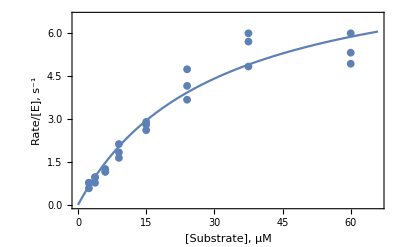

```mathematica
ModifiedMM=kcat/(1+kcat/(ksp * s));
Model=NonlinearModelFit[avgData,{ModifiedMM,kcat>0,ksp>0},{kcat,ksp},s];
modeldata=Model["ParameterTable"]
sMax=1.1*Max[fullData[[All,1]]];
Show[
ListPlot[fullData,PlotRange->{{0,sMax},{0,1.1*Max[fullData[[All,2]]]}},
Frame->True,PlotMarkers->{Automatic,8},
FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],
Plot[Model[s],{s,0,sMax}],LabelStyle->Directive[Bold,Medium]]
```

## Use data from the model

```mathematica
modeldata(*showing the table again as a reminder*)
```

| Estimate | Standard Error | t-Statistic | P-Value
kcat | 8.74556 | 1.11101 | 7.8717 | 0.000222538
ksp | 0.294779 | 0.0416145 | 7.08357 | 0.000397047

```mathematica
kcatbestfitvalue=8.745560188093302;
kspbestfitvalue=0.29477938924225716;
kcatstandarderror=1.1110132625333924;
kspstandarderror=0.04161453957010604;
Kmbestfitvalue=kcatbestfitvalue/kspbestfitvalue;
out1=Row[{"Km = ",Kmbestfitvalue," µM"}];
TextCell[out1,CellFrame->True]
Kmstandarderror=Kmbestfitvalue*√((kcatstandarderror/kcatbestfitvalue)^2+(kspstandarderror/kspbestfitvalue)^2);
out2=Row[{"Km std error = ",Kmstandarderror," µM"}];
TextCell[out2,CellFrame->True]
kspSF=ScientificForm[kspbestfitvalue*10^6];
out3=Row[{"ksp = ",kspSF," M-1s-1"}];
TextCell[out3,CellFrame->True]
kspSFerror=ScientificForm[kspstandarderror*10^6];
out4=Row[{"ksp std error = ",kspSFerror," M-1s-1"}];
TextCell[out4,CellFrame->True]
kcatpercenterror=100*kcatstandarderror/kcatbestfitvalue;
out5=Row[{"kcat percent error = ",kcatpercenterror," %"}];
TextCell[out5,CellFrame->True]
Kmpercenterror=100*Kmstandarderror/Kmbestfitvalue;
out6=Row[{"Km percent error = ",Kmpercenterror," %"}];
TextCell[out6,CellFrame->True]
ksppercenterror=100*kspstandarderror/kspbestfitvalue;
out7=Row[{"ksp percent error = ",ksppercenterror," %"}];
TextCell[out7,CellFrame->True]
```

Km = 29.6682 µM

Km std error = 5.63445 µM

ksp = 2.94779×10^5 M-1s-1

ksp std error = 4.16145×10^4 M-1s-1

kcat percent error = 12.7037 %

Km percent error = 18.9916 %

ksp percent error = 14.1172 %

## Alternative binding equations

{{1.02342,0.0906551}, | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.02342 | 0.418963 | 2.44274 | 0.0502839
S | 0.0906551 | 0.0153702 | 5.89811 | 0.00105503}

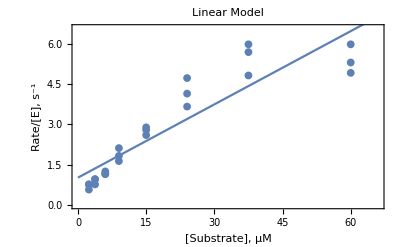

{{1.02342,0.0906551}, | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.02342 | 0.418963 | 2.44274 | 0.0502839
S | 0.0906551 | 0.0153702 | 5.89811 | 0.00105503}

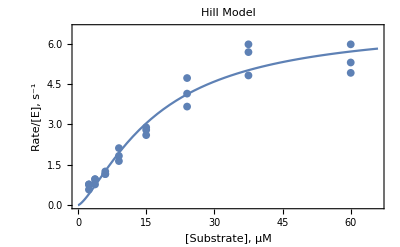

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{kcat→6.72225,kspH→0.390078,n→1.38322}, | Estimate | Standard Error | t-Statistic | P-Value
kcat | 6.72225 | 0.935269 | 7.18751 | 0.000811537
kspH | 0.390078 | 0.0535233 | 7.28801 | 0.000761056
n | 1.38322 | 0.268511 | 5.15145 | 0.00361051}

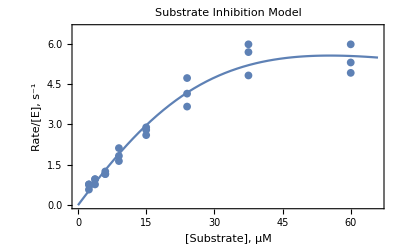

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{kcat→49.9998,ksp→0.22558,KI→13.8514}, | Estimate | Standard Error | t-Statistic | P-Value
kcat | 49.9998 | 86.4483 | 0.578378 | 0.588082
ksp | 0.22558 | 0.0256364 | 8.79924 | 0.000314617
KI | 13.8514 | 28.6328 | 0.483759 | 0.648999}

```mathematica
LinearModel=LinearModelFit[avgData,S,S];
LinearModel[{"BestFitParameters","ParameterTable"}]
Show[ListPlot[{fullData},PlotRange->{{0,sMax},{0,1.1*Max[fullData[[All,2]]]}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{LinearModel[S]},{S,0,sMax}],LabelStyle->Directive[Bold,12],PlotLabel->"Linear Model"]
Hill=(kcat)/(1+(kcat/(kspH*S))^n);
HillModel=NonlinearModelFit[avgData,{Hill, kcat>0,kspH>0,n>0},{kcat,kspH,n},S];
HillModel[{"BestFitParameters","ParameterTable"}]
Show[ListPlot[{fullData},PlotRange->{{0,sMax},{0,1.1*Max[fullData[[All,2]]]}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{HillModel[S]},{S,0,sMax}],LabelStyle->Directive[Bold,12],PlotLabel->"Hill Model"]
SubInh=(kcat)/(1+kcat/(ksp*S)+S/KI);
SubInhModel=NonlinearModelFit[avgData,{SubInh, kcat>0,ksp>0,KI>0,kcat<50,KI>10},{kcat,ksp,KI},S];
SubInhModel[{"BestFitParameters","ParameterTable"}]
Show[ListPlot[{fullData},PlotRange->{{0,sMax},{0,1.1*Max[fullData[[All,2]]]}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{SubInhModel[S]},{S,0,sMax}],LabelStyle->Directive[Bold,12],PlotLabel->"Substrate Inhibition Model"]
```